```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h,k,ff,kk,ll,x,a,s0]
```

```mathematica
(*Middle 5th Cantor Cartoon*)
```

```mathematica
f[x_]:=1/;0<=x<=1/5
f[x_]:=1/;1/5<x<=2/5
f[x_]:=0/;2/5<x≤3/5
f[x_]:=1/;3/5<x≤4/5
f[x_]:=1/;4/5<x<=1
```

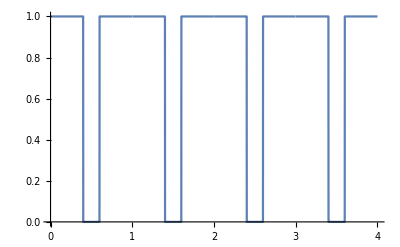

```mathematica
ff[x_]=f[Mod[Abs[x],1]];
Plot[ff[x],{x,0,4}]
s0=N[Log[2]/Log[5]];
```

```mathematica
kk[x_]=Sum[ff[5^k*x]/5^(s0*k),{k,0,20}];
ll[x_]=Sum[ff[5^k*x+1/3]/5^(s0*k),{k,0,20}];
mm[x_]=Sum[ff[5^k*x-1/3]/5^(s0*k),{k,0,20}];
```

```mathematica
b=ParallelTable[{ll[x],kk[x],mm[x]},{x,0,1,1/800000}];
```

```mathematica
g1=ListPointPlot3D[b,Axes->False,PlotStyle->PointSize[0.001],ColorFunction->"DarkRainbow",ImageSize->{2000,2000},ViewPoint->{2,2,2},Background->Black];
```

```mathematica
Export["Biscuit_Cantor_3part_phase3rdsscale5_250000_Grid_BackBlack_g1.jpg",g1];
```

```mathematica
g2=Show[g1,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Cantor_3part_phase3rdsscale5_250000_Grid_BackBlack_g2.jpg",g2];
```

```mathematica
g3=Show[g1,ViewPoint->Front,ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Cantor_3part_phase3rdsscale5_250000_Grid_BackBlack_g3.jpg",g3];
```

```mathematica
g4=Show[g1,ViewPoint->{1.,-2,-2},ImageSize->{2000,2000}];
```

```mathematica
Export["Biscuit_Cantor_3part_phase3rdsscale5_250000_Grid_BackBlack_g4.jpg",g4];
```

```mathematica
(*end*)
```